```mathematica
"HEAT EQUATION. CRANK-NICOLSON METHOD"
```

```mathematica
Question: The one-dimension heat equation ut=c^2uxx is a parabolic equation that governs, for instance,  the heat flow in a bar where u(x,t) is the temperature at a point x and time t. Solve the corresponding difference equation with c^2=1 on the interval 0≤x≤1 (the bar extending from x=0 to x=1 along the x-axis) subject to initial temperature u(x,0 )=sin(pix) by the Crank-Nicolson method with x-step h=0.2 and time step k=0.04 doing 5 time steps.
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
n=4; r=1; h=0.2;
```

```mathematica
A=Table[Switch[j-k, 0 ,4 , 1, -1, -1, -1, _, 0], {j, n}, {k,n}];
```

```mathematica
MatrixForm[A]
```

(4 | -1 | 0 | 0
-1 | 4 | -1 | 0
0 | -1 | 4 | -1
0 | 0 | -1 | 4)

```mathematica
Do[u[k]=N[Sin[Pi k h]], {k, 0, n+1}]
```

```mathematica
Table[u[k], {k, 0, n+1}]
```

{0.,0.587785,0.951057,0.951057,0.587785,1.22465×10^-16}

```mathematica
T0=Table[{0.2 k, u[k]}, {k, 0, n+1}]
```

{{0.,0.},{0.2,0.587785},{0.4,0.951057},{0.6,0.951057},{0.8,0.587785},{1.,1.22465×10^-16}}

```mathematica
Table[Temp[k], {k,1, n+1}];
```

```mathematica
M=5;
```

```mathematica
Do[
   b=Table[0, {i, 1, n}];
   Do[b[[k]]=u[k-1]+u[k+1], {k, 1, n}];
   v=N[LinearSolve[A, b]];
            Print[v]; Temp[j]=v;
    Do[u[k]=v[[k]], {k, 1, n}],
    {j, 1, M}
    ];
```

{0.399274,0.646039,0.646039,0.399274}

{0.271221,0.438844,0.438844,0.271221}

{0.184236,0.2981,0.2981,0.184236}

{0.125149,0.202495,0.202495,0.125149}

{0.0850118,0.137552,0.137552,0.0850118}

```mathematica
v=Table[Table[Temp[k][[j]], {j, 1, M-1}], {k, 1, n+1}]
```

{{0.399274,0.646039,0.646039,0.399274},{0.271221,0.438844,0.438844,0.271221},{0.184236,0.2981,0.2981,0.184236},{0.125149,0.202495,0.202495,0.125149},{0.0850118,0.137552,0.137552,0.0850118}}

```mathematica
v[[3]]
```

{0.184236,0.2981,0.2981,0.184236}

```mathematica
v[[3,2]]
```

0.2981

```mathematica
w=Table[Join[{0}, v[[j]], {0}], {j, 1, M}]
```

{{0,0.399274,0.646039,0.646039,0.399274,0},{0,0.271221,0.438844,0.438844,0.271221,0},{0,0.184236,0.2981,0.2981,0.184236,0},{0,0.125149,0.202495,0.202495,0.125149,0},{0,0.0850118,0.137552,0.137552,0.0850118,0}}

```mathematica
w[[1]]
```

{0,0.399274,0.646039,0.646039,0.399274,0}

```mathematica
T=Table[Table[{0.2 i, w[[p]][[i+1]]}, {i, 0, n+1}], {p, 1, M}]
```

{{{0.,0},{0.2,0.399274},{0.4,0.646039},{0.6,0.646039},{0.8,0.399274},{1.,0}},{{0.,0},{0.2,0.271221},{0.4,0.438844},{0.6,0.438844},{0.8,0.271221},{1.,0}},{{0.,0},{0.2,0.184236},{0.4,0.2981},{0.6,0.2981},{0.8,0.184236},{1.,0}},{{0.,0},{0.2,0.125149},{0.4,0.202495},{0.6,0.202495},{0.8,0.125149},{1.,0}},{{0.,0},{0.2,0.0850118},{0.4,0.137552},{0.6,0.137552},{0.8,0.0850118},{1.,0}}}

```mathematica
T[[1]]
```

{{0.,0},{0.2,0.399274},{0.4,0.646039},{0.6,0.646039},{0.8,0.399274},{1.,0}}

```mathematica
x=Table[x,{x,0,1,0.2}]
```

{0.,0.2,0.4,0.6,0.8,1.}

```mathematica
U=Table[Sin[Pi k h], {k, 0, n+1}]
```

{0.,0.587785,0.951057,0.951057,0.587785,1.22465×10^-16}

```mathematica
W=Transpose[w]
```

{{0,0,0,0,0},{0.399274,0.271221,0.184236,0.125149,0.0850118},{0.646039,0.438844,0.2981,0.202495,0.137552},{0.646039,0.438844,0.2981,0.202495,0.137552},{0.399274,0.271221,0.184236,0.125149,0.0850118},{0,0,0,0,0}}

```mathematica
table=Table[{x[[l]],U[[l]],W[[l,1]],W[[l,2]],W[[l,3]],W[[l,4]],W[[l,5]]},{l,1,6}]
```

{{0.,0.,0,0,0,0,0},{0.2,0.587785,0.399274,0.271221,0.184236,0.125149,0.0850118},{0.4,0.951057,0.646039,0.438844,0.2981,0.202495,0.137552},{0.6,0.951057,0.646039,0.438844,0.2981,0.202495,0.137552},{0.8,0.587785,0.399274,0.271221,0.184236,0.125149,0.0850118},{1.,1.22465×10^-16,0,0,0,0,0}}

```mathematica
table1=Prepend[table,{"x","u(x,t),t=0","u(x,t),t=0.04","u(x,t),t=0.08","u(x,t),t=0.12","u(x,t),t=0.16","u(x,t),t=0.20"}]
```

{{x,u(x,t),t=0,u(x,t),t=0.04,u(x,t),t=0.08,u(x,t),t=0.12,u(x,t),t=0.16,u(x,t),t=0.20},{0.,0.,0,0,0,0,0},{0.2,0.587785,0.399274,0.271221,0.184236,0.125149,0.0850118},{0.4,0.951057,0.646039,0.438844,0.2981,0.202495,0.137552},{0.6,0.951057,0.646039,0.438844,0.2981,0.202495,0.137552},{0.8,0.587785,0.399274,0.271221,0.184236,0.125149,0.0850118},{1.,1.22465×10^-16,0,0,0,0,0}}

```mathematica
Grid[table1, Frame->All,Spacings->{1, 1}]
```

x | u(x,t),t=0 | u(x,t),t=0.04 | u(x,t),t=0.08 | u(x,t),t=0.12 | u(x,t),t=0.16 | u(x,t),t=0.20
0. | 0. | 0 | 0 | 0 | 0 | 0
0.2 | 0.587785 | 0.399274 | 0.271221 | 0.184236 | 0.125149 | 0.0850118
0.4 | 0.951057 | 0.646039 | 0.438844 | 0.2981 | 0.202495 | 0.137552
0.6 | 0.951057 | 0.646039 | 0.438844 | 0.2981 | 0.202495 | 0.137552
0.8 | 0.587785 | 0.399274 | 0.271221 | 0.184236 | 0.125149 | 0.0850118
1. | 1.22465×10^-16 | 0 | 0 | 0 | 0 | 0

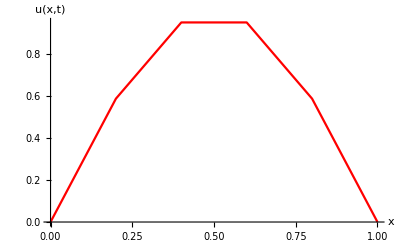

```mathematica
P0=ListLinePlot[T0,PlotStyle->Red, AxesLabel->{"x", "u(x,t)"}]
```

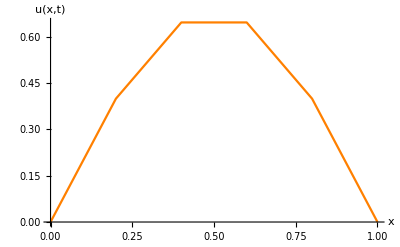

```mathematica
P1=ListLinePlot[T[[1]],PlotStyle->Orange, AxesLabel->{"x", "u(x,t)"}]
```

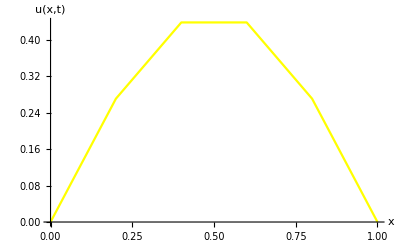

```mathematica
P2=ListLinePlot[T[[2]],PlotStyle->Yellow, AxesLabel->{"x", "u(x,t)"}]
```

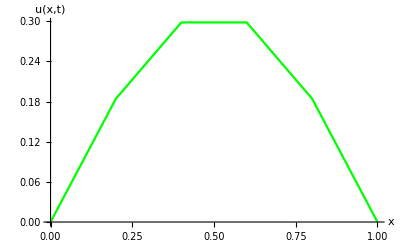

```mathematica
P3=ListLinePlot[T[[3]],PlotStyle->Green, AxesLabel->{"x", "u(x,t)"}]
```

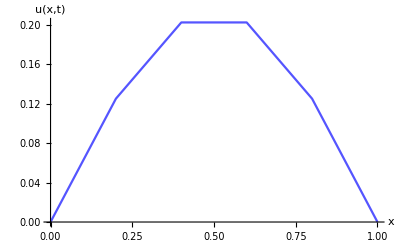

```mathematica
P4=ListLinePlot[T[[4]],PlotStyle->Lighter[Blue], AxesLabel->{"x", "u(x,t)"}]
```

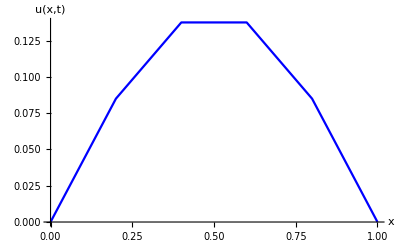

```mathematica
P5=ListLinePlot[T[[5]],PlotStyle->Blue, AxesLabel->{"x", "u(x,t)"}]
```

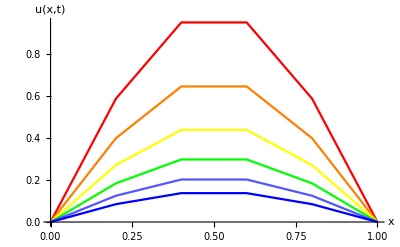

```mathematica
Show[P0, P1, P2, P3, P4, P5, PlotRange->Automatic]
```

```mathematica
S0=Graphics[{BSplineCurve[T0],Red, Line[T0],Red, Point[T0]}, Axes->True, AxesLabel->{"x", "u(x,t)"}]
```

-Graphics-

```mathematica
S1=Graphics[{BSplineCurve[T[[1]]], Orange, Line[T[[1]]], Red, Point[T[[1]]]}, Axes->True, AxesLabel->{"x", "u(x,t)"}]
```

-Graphics-

```mathematica
S2=Graphics[{BSplineCurve[T[[2]]], Yellow, Line[T[[2]]], Red, Point[T[[2]]]}, Axes->True, AxesLabel->{"x", "u(x,t)"}]
```

-Graphics-

```mathematica
S3=Graphics[{BSplineCurve[T[[3]]], Green, Line[T[[3]]], Red, Point[T[[3]]]}, Axes->True, AxesLabel->{"x", "u(x,t)"}]
```

-Graphics-

```mathematica
S4=Graphics[{BSplineCurve[T[[4]]], Lighter[Blue], Line[T[[4]]], Red, Point[T[[4]]]}, Axes->True, AxesLabel->{"x", "u(x,t)"}]
```

-Graphics-

```mathematica
S5=Graphics[{BSplineCurve[T[[5]]], Blue, Line[T[[5]]], Red, Point[T[[5]]]}, Axes->True, AxesLabel->{"x", "u(x,t)"}]
```

-Graphics-

```mathematica
Show[S0, S1, S2, S3, S4, S5]
```

-Graphics-

```mathematica
Another Question: Solve the corresponding difference equation with c^2 = 1 on the interval 0≤ x≤ 1 subject to the initial temperature u(x,0)=sin(pix) by Crank-Nicolson method with x-steps h=0.25 and time t-step k=0.5 doing 5 time steps.
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
n=3; r=8; h=0.25;
```

```mathematica
A=Table[Switch[j-k,0, 18, 1,-8,-1,-8,_, 0], {j, n}, {k,n}];
```

```mathematica
MatrixForm[A]
```

(18 | -8 | 0
-8 | 18 | -8
0 | -8 | 18)

```mathematica
Do[u[k]=N[Sin[Pi k h]], {k, 0, n+1}]
```

```mathematica
Table[u[k], {k, 0, n+1}]
```

{0.,0.707107,1.,0.707107,1.22465×10^-16}

```mathematica
T0=Table[{0.25 k, u[k]}, {k, 0, n+1}]
```

{{0.,0.},{0.25,0.707107},{0.5,1.},{0.75,0.707107},{1.,1.22465×10^-16}}

```mathematica
Table[Temp[k], {k,1, n+1}];
```

```mathematica
M=4;
```

```mathematica
Do[
   b=Table[0, {i, 1, n}];
   Do[b[[k]]=u[k-1]+u[k+1], {k, 1, n}];
   v=N[LinearSolve[A, b]];
            Print[v]; Temp[j]=v;
    Do[u[k]=v[[k]], {k, 1, n}],
    {j, 1, M}
    ];
```

{0.14956,0.211509,0.14956}

{0.0316333,0.0447362,0.0316333}

{0.00669074,0.00946213,0.00669074}

{0.00141515,0.00200133,0.00141515}

```mathematica
v=Table[Table[Temp[k][[j]], {j, 1, M-1}], {k, 1, n+1}]
```

{{0.14956,0.211509,0.14956},{0.0316333,0.0447362,0.0316333},{0.00669074,0.00946213,0.00669074},{0.00141515,0.00200133,0.00141515}}

```mathematica
v[[1]]
```

{0.14956,0.211509,0.14956}

```mathematica
v[[1,3]]
```

0.14956

```mathematica
w=Table[Join[{0}, v[[j]], {0}], {j, 1, M}]
```

{{0,0.14956,0.211509,0.14956,0},{0,0.0316333,0.0447362,0.0316333,0},{0,0.00669074,0.00946213,0.00669074,0},{0,0.00141515,0.00200133,0.00141515,0}}

```mathematica
w[[3]]
```

{0,0.00669074,0.00946213,0.00669074,0}

```mathematica
T=Table[Table[{0.25 i, w[[p]][[i+1]]}, {i, 0, n+1}], {p, 1, M}]
```

{{{0.,0},{0.25,0.14956},{0.5,0.211509},{0.75,0.14956},{1.,0}},{{0.,0},{0.25,0.0316333},{0.5,0.0447362},{0.75,0.0316333},{1.,0}},{{0.,0},{0.25,0.00669074},{0.5,0.00946213},{0.75,0.00669074},{1.,0}},{{0.,0},{0.25,0.00141515},{0.5,0.00200133},{0.75,0.00141515},{1.,0}}}

```mathematica
T[[2]]
```

{{0.,0},{0.25,0.0316333},{0.5,0.0447362},{0.75,0.0316333},{1.,0}}

```mathematica
x=Table[x,{x,0,1,0.25}]
```

{0.,0.25,0.5,0.75,1.}

```mathematica
U=Table[Sin[Pi k h], {k, 0, n+1}]
```

{0.,0.707107,1.,0.707107,1.22465×10^-16}

```mathematica
W=Transpose[w]
```

{{0,0,0,0},{0.14956,0.0316333,0.00669074,0.00141515},{0.211509,0.0447362,0.00946213,0.00200133},{0.14956,0.0316333,0.00669074,0.00141515},{0,0,0,0}}

```mathematica
table=Table[{x[[l]],U[[l]],W[[l,1]],W[[l,2]],W[[l,3]],W[[l,4]]},{l,1,5}]
```

{{0.,0.,0,0,0,0},{0.25,0.707107,0.14956,0.0316333,0.00669074,0.00141515},{0.5,1.,0.211509,0.0447362,0.00946213,0.00200133},{0.75,0.707107,0.14956,0.0316333,0.00669074,0.00141515},{1.,1.22465×10^-16,0,0,0,0}}

```mathematica
table1=Prepend[table,{"x","u(x,t),t=0","u(x,t),t=0.5","u(x,t),t=1.0","u(x,t),t=1.5","u(x,t),t=2.0"}]
```

{{x,u(x,t),t=0,u(x,t),t=0.5,u(x,t),t=1.0,u(x,t),t=1.5,u(x,t),t=2.0},{0.,0.,0,0,0,0},{0.25,0.707107,0.14956,0.0316333,0.00669074,0.00141515},{0.5,1.,0.211509,0.0447362,0.00946213,0.00200133},{0.75,0.707107,0.14956,0.0316333,0.00669074,0.00141515},{1.,1.22465×10^-16,0,0,0,0}}

```mathematica
Grid[table1, Frame->All,Spacings->{1, 1}]
```

x | u(x,t),t=0 | u(x,t),t=0.5 | u(x,t),t=1.0 | u(x,t),t=1.5 | u(x,t),t=2.0
0. | 0. | 0 | 0 | 0 | 0
0.25 | 0.707107 | 0.14956 | 0.0316333 | 0.00669074 | 0.00141515
0.5 | 1. | 0.211509 | 0.0447362 | 0.00946213 | 0.00200133
0.75 | 0.707107 | 0.14956 | 0.0316333 | 0.00669074 | 0.00141515
1. | 1.22465×10^-16 | 0 | 0 | 0 | 0

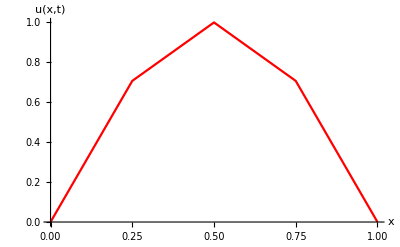

```mathematica
P0=ListLinePlot[T0,PlotStyle->Red, AxesLabel->{"x", "u(x,t)"}]
```

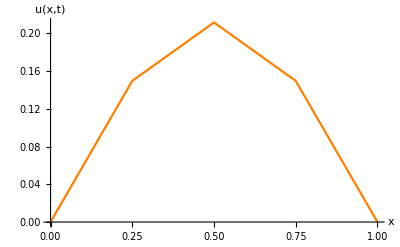

```mathematica
P1=ListLinePlot[T[[1]],PlotStyle->Orange, AxesLabel->{"x", "u(x,t)"}]
```

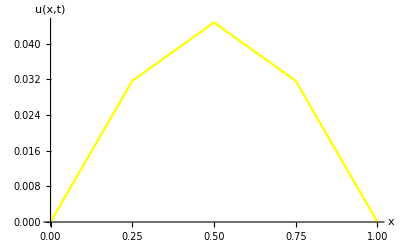

```mathematica
P2=ListLinePlot[T[[2]],PlotStyle->Yellow, AxesLabel->{"x", "u(x,t)"}]
```

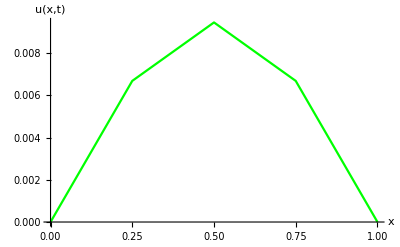

```mathematica
P3=ListLinePlot[T[[3]],PlotStyle->Green, AxesLabel->{"x", "u(x,t)"}]
```

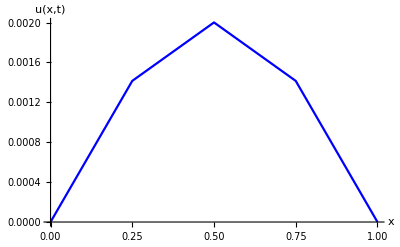

```mathematica
P4=ListLinePlot[T[[4]],PlotStyle->Blue, AxesLabel->{"x", "u(x,t)"}]
```

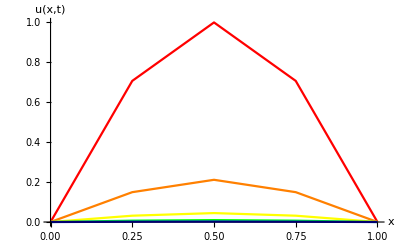

```mathematica
Show[P0, P1, P2, P3, P4, PlotRange->All]
```

```mathematica
S0=Graphics[{BSplineCurve[T0], Red, Line[T0], Red, Point[T0]}, Axes->True, AxesLabel->{"x", "u(x,t)"}];
```

```mathematica
S1=Graphics[{BSplineCurve[T[[1]]],Orange, Line[T[[1]]], Red, Point[T[[1]]]}, Axes->True, AxesLabel->{"x", "u(x,t)"}];
```

```mathematica
S2=Graphics[{BSplineCurve[T[[2]]], Yellow, Line[T[[2]]], Red, Point[T[[2]]]}, Axes->True, AxesLabel->{"x", "u(x,t)"}];
```

```mathematica
S3=Graphics[{BSplineCurve[T[[3]]], Green, Line[T[[3]]], Red, Point[T[[3]]]}, Axes->True, AxesLabel->{"x", "u(x,t)"}];
```

```mathematica
S4=Graphics[{BSplineCurve[T[[4]]],Blue, Line[T[[4]]], Red, Point[T[[4]]]}, Axes->True, AxesLabel->{"x", "u(x,t)"}];
```

```mathematica
Show[S0, S1, S2, S3, S4]
```

-Graphics-

```mathematica
ClearAll["Global`*"]
```